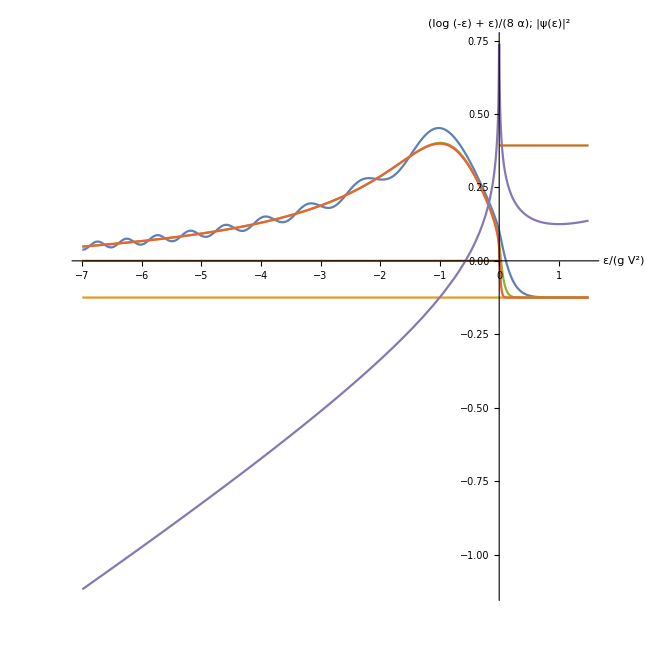

```mathematica
start =1.5;finish=-12;α1=0.1;E2=0.5;s121=ψ0[x]/.NDSolve[{0== E2 ψ0[x]-α1 ψ0''[x]+ψ0[x](Log[-x-I*10^(-5)])+x ψ0[x],ψ0[start]==0,ψ0'[start]==0.001},ψ0,{x,start,finish}];nr1=(NIntegrate[Abs[s121^2],{x,finish,finish+0.5}]/0.5);α2=0.01;
s122=ψ0[x]/.NDSolve[{0== E2 ψ0[x]-α2  ψ0''[x]+ψ0[x](Log[-x-I*10^(-5)])+x ψ0[x],ψ0[start]==0,ψ0'[start]==0.001},ψ0,{x,start,finish}];nr2=(NIntegrate[Abs[s122^2],{x,finish,finish+0.5}]/0.5);α3=0.001;
s123=ψ0[x]/.NDSolve[{0== E2 ψ0[x]-α3  ψ0''[x]+ψ0[x](Log[-x-I*10^(-5)])+x ψ0[x],ψ0[start]==0,ψ0'[start]==0.001},ψ0,{x,start,finish}];nr3=(NIntegrate[Abs[s123^2],{x,finish,finish+0.5}]/0.5);
Plot[{-E2/(4)+Abs[s121^2]/(8 nr1),-E2/(4),-E2/(4)+Abs[s122^2]/(8 nr2),-E2/(4)+Abs[s123^2]/(8 nr3),Re[-1.(Log[x-I*10^(-5)])+x]/(8),Im[-1.(Log[-x-I*10^(-5)])+x]/(8)},{x,start,-7},PlotRange->All,AspectRatio->1,AxesLabel->{ε/(g V^2),"(log (-ε) + ε)/(8  α); |ψ(ε)|^2"}]
```

```mathematica
Export["figure13.eps",-Graphics-]
```

figure13.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["figure13.eps"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["figure13.eps"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["figure13.eps"]]]
```

```mathematica
SystemOpen["figure13.eps"]
```

```mathematica
SystemOpen["figure13.eps"]
```

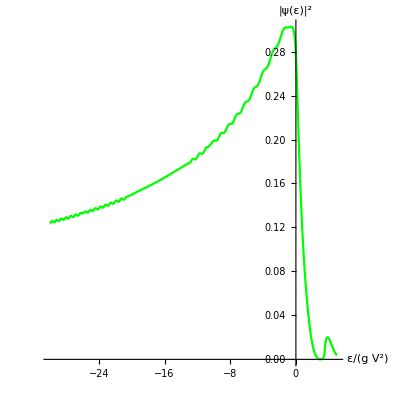

```mathematica
start =25;finish=-30;α=1;E2=-5;s122=ψ0[x]/.NDSolve[{0== E2 ψ0[x]-α ψ0''[x]+ψ0[x](Log[-x-I*10^(-5)]-3/(x-3.5+I*10^(-5)))+x ψ0[x],ψ0[start]==0,ψ0'[start]==0.001},ψ0,{x,start,finish}];nr2=(NIntegrate[Abs[s122^2],{x,finish,finish+0.5}]/0.5);
Plot[Abs[s122^2]/(8α nr2),{x,-30,5},PlotRange->All,AspectRatio->1,AxesLabel->{ε/(g V^2),"|ψ(ε)|^2"},PlotStyle->RGBColor[0,1,0]]
```

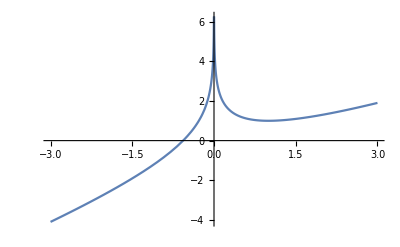

```mathematica
Plot[Re[x-Log[-x+I*10^(-5)]],{x,-3,3}]
```

```mathematica
start =25;finish=-30;α=1;E2=-5;s122=ψ0[x]/.NDSolve[{0== E2 ψ0[x]-α ψ0''[x]+ψ0[x](Log[-x-I*10^(-5)]-10/(x-2+I*10^(-5)))+x ψ0[x],ψ0[start]==0,ψ0'[start]==0.001},ψ0,{x,start,finish}];nr2=(NIntegrate[Abs[s122^2],{x,finish,finish+0.5}]/0.5);
```

Plot[Abs[s122^2]/(8 α nr2),{x,-20,10},PlotRange→All,AspectRatio→1,AxesLabel→{ε/(g V^2),|ψ(ε)|^2},PlotStyle→RGBColor[0.1, 0.1, 0.1],ListPlot[{Callout[{2,0},Spoiler position]},PlotStyle→{Red}]]

```mathematica
Show[Plot[Abs[s122^2]/(8α nr2),{x,-20,10},PlotRange->All,AspectRatio->1,AxesLabel->{ε/(g V^2),"|ψ(ε)|^2"},PlotStyle->RGBColor[0.1,0.1,0.1]],ListPlot[{Callout[{2,0},"Spoiler position"]},PlotStyle->{Red}]]
```

-Graphics-

```mathematica
Export["spoilerstate.eps",-Graphics-]
```

spoilerstate.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["spoilerstate.eps"]]]
```

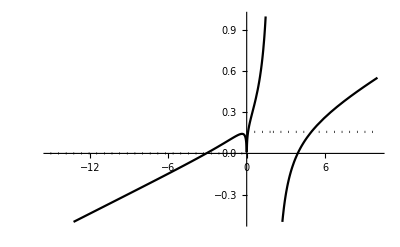

```mathematica
plt5=Plot[{Re[(Log[-x+I*10^(-5)]-10/(x-2+I*10^(-5)))+x]/20,Im[(Log[-x+I*10^(-5)]-10/(x-2+I*10^(-10)))+x]/20},{x,-15,10},PlotRange->{-0.5,1},PlotStyle->{RGBColor[0,0,0],{RGBColor[0,0,0],Dotted}}]
```

```mathematica
Show[Plot[Abs[s122^2]/(8α nr2),{x,-15,10},PlotRange->{-0.5,1},AspectRatio->1,AxesLabel->{ε/(g V^2),"|ψ(ε)|^2"},PlotStyle->RGBColor[0,1,0]],plt5,ListPlot[{Callout[{2,0},"Spoiler position"]},PlotStyle->{Red}]]
```

-Graphics-

```mathematica
Export["spoilerstate.eps",-Graphics-]
```

spoilerstate.eps

```mathematica
start =25;
finish=-30;
α=1;
E2=-5;
listoflists={};
For[j=2,j<4,j+=0.5,list={};For[i=1,i<15,i++,spick1=ψ0[x]/.NDSolve[{0== E2 ψ0[x]-α ψ0''[x]+ψ0[x](Log[-x-I*10^(-5)]-i/(x-j+I*10^(-5)))+x ψ0[x],ψ0[start]==0,ψ0'[start]==0.001},ψ0,{x,start,finish}];AppendTo[list,spick1]];AppendTo[listoflists,list]]
```

```mathematica
Table[NIntegrate[Abs[listoflists[[i]][[j]]]^2 ,{x,i*0.5+2,5}]/NIntegrate[Abs[listoflists[[i]][[j]]]^2,{x,0,i*0.5+2}],{i,4},{j,14}]
```

{{{0.0787476},{0.326265},{0.946276},{1.79023},{2.1567},{2.24695},{2.32775},{2.12784},{1.64281},{1.13289},{0.722272},{0.438321},{0.260308},{0.153615}},{{0.0283831},{0.169948},{0.565399},{1.13884},{1.58329},{0.948456},{0.50277},{0.263088},{0.131611},{0.0652572},{0.0328095},{0.0168131},{0.00880385},{0.00470603}},{{0.00776929},{0.0748766},{0.597715},{0.223987},{0.141637},{0.0699088},{0.0304826},{0.0135807},{0.006197},{0.00288188},{0.00136626},{0.000660315},{0.000325407},{0.000163602}},{{0.00147343},{0.00898536},{0.0467194},{0.0158408},{0.00668111},{0.0030417},{0.00134654},{0.000592772},{0.000263428},{0.000118673},{0.0000542866},{0.0000252246},{0.0000119048},{5.70909×10^-6}}}

```mathematica
matrix10={{{0.07874758653427479},{0.3262646929790627},{0.9462761968491167},{1.7902284172093121},{2.156696698274851},{2.2469503654254517},{2.327749476911791},{2.1278425194768413},{1.6428108446453586},{1.1328883032340664},{0.7222721649668867},{0.4383211746105653},{0.260308402904246},{0.15361546055374098}},{{0.028383071115153573},{0.1699482168985642},{0.5653985461297029},{1.1388381270909194},{1.5832885845098625},{0.9484556730277268},{0.5027702818115473},{0.26308760946221643},{0.1316106357129398},{0.0652572280481026},{0.03280954663711038},{0.016813127164957933},{0.008803852288513606},{0.004706025005946372}},{{0.00776929486758738},{0.07487659129276379},{0.5977152868141876},{0.223986701571324},{0.14163661501014052},{0.06990884781563743},{0.030482648953153654},{0.013580703619982466},{0.0061970046144808905},{0.002881878280768616},{0.0013662604470442601},{0.0006603150101330267},{0.0003254068531940119},{0.00016360176280720662}},{{0.0014734327863818867},{0.00898535889623844},{0.04671944790508477},{0.01584076671674407},{0.006681106328515282},{0.0030416979708574434},{0.0013465412984941295},{0.0005927717617651993},{0.00026342754576479924},{0.00011867297030451854},{0.00005428662483282256},{0.000025224607367206643},{0.000011904824233119798},{5.709090403187112*^-6}}}
```

{{{0.0787476},{0.326265},{0.946276},{1.79023},{2.1567},{2.24695},{2.32775},{2.12784},{1.64281},{1.13289},{0.722272},{0.438321},{0.260308},{0.153615}},{{0.0283831},{0.169948},{0.565399},{1.13884},{1.58329},{0.948456},{0.50277},{0.263088},{0.131611},{0.0652572},{0.0328095},{0.0168131},{0.00880385},{0.00470603}},{{0.00776929},{0.0748766},{0.597715},{0.223987},{0.141637},{0.0699088},{0.0304826},{0.0135807},{0.006197},{0.00288188},{0.00136626},{0.000660315},{0.000325407},{0.000163602}},{{0.00147343},{0.00898536},{0.0467194},{0.0158408},{0.00668111},{0.0030417},{0.00134654},{0.000592772},{0.000263428},{0.000118673},{0.0000542866},{0.0000252246},{0.0000119048},{5.70909×10^-6}}}

```mathematica
matrix11=ArrayReshape[matrix10,{4,14}]
```

{{0.0787476,0.326265,0.946276,1.79023,2.1567,2.24695,2.32775,2.12784,1.64281,1.13289,0.722272,0.438321,0.260308,0.153615},{0.0283831,0.169948,0.565399,1.13884,1.58329,0.948456,0.50277,0.263088,0.131611,0.0652572,0.0328095,0.0168131,0.00880385,0.00470603},{0.00776929,0.0748766,0.597715,0.223987,0.141637,0.0699088,0.0304826,0.0135807,0.006197,0.00288188,0.00136626,0.000660315,0.000325407,0.000163602},{0.00147343,0.00898536,0.0467194,0.0158408,0.00668111,0.0030417,0.00134654,0.000592772,0.000263428,0.000118673,0.0000542866,0.0000252246,0.0000119048,5.70909×10^-6}}

```mathematica
list15={}
For[j=2,j<4,j+=0.5,For[i=0,i<14,i++;AppendTo[list15,{i+1,j,Log[matrix11[[1+(j-2)*2]][[i]]]}]]]
```

{}

```mathematica
list15
```

{{2,2,-2.54151},{3,2,-1.12005},{4,2,-0.0552208},{5,2,0.582343},{6,2,0.768578},{7,2,0.809574},{8,2,0.844902},{9,2,0.755109},{10,2,0.496409},{11,2,0.12477},{12,2,-0.325353},{13,2,-0.824803},{14,2,-1.34589},{15,2,-1.8733},{2,2.5,-3.56196},{3,2.5,-1.77226},{4,2.5,-0.570224},{5,2.5,0.130009},{6,2.5,0.459504},{7,2.5,-0.0529202},{8,2.5,-0.687622},{9,2.5,-1.33527},{10,2.5,-2.02791},{11,2.5,-2.72942},{12,2.5,-3.41704},{13,2.5,-4.0856},{14,2.5,-4.73257},{15,2.5,-5.35891},{2,3.,-4.85758},{3,3.,-2.59191},{4,3.,-0.514641},{5,3.,-1.49617},{6,3.,-1.95449},{7,3.,-2.66056},{8,3.,-3.4906},{9,3.,-4.29911},{10,3.,-5.08369},{11,3.,-5.84931},{12,3.,-6.59568},{13,3.,-7.32279},{14,3.,-8.03043},{15,3.,-8.71808},{2,3.5,-6.52016},{3,3.5,-4.71216},{4,3.5,-3.06359},{5,3.5,-4.14517},{6,3.5,-5.00847},{7,3.5,-5.79534},{8,3.5,-6.61022},{9,3.5,-7.4307},{10,3.5,-8.24173},{11,3.5,-9.03914},{12,3.5,-9.82123},{13,3.5,-10.5877},{14,3.5,-11.3386},{15,3.5,-12.0735}}

```mathematica
plt=ListPlot3D[list15,AxesLabel->{ "(|SubscriptBox[v, s]|)^2/(g SuperscriptBox[V, 2])^2","E_s/(g SuperscriptBox[V, 2])","Log((∫_E_0^∞)/(∫_0^E_0))"},AxesStyle->Italic,InterpolationOrder->10,Boxed->False,PlotLabel->"E_0/(g SuperscriptBox[V, 2])=5, Log((√α)/(g SuperscriptBox[V, 2]))=0"]
```

-Graphics3D-

```mathematica
Export["figure16.eps",-Graphics3D-]
```

figure16.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["figure16.eps"]]]
```

```mathematica
Table[NIntegrate[x Abs[listoflists[[i]][[j]]]^2 ,{x,0,i*0.5+2}]/NIntegrate[Abs[listoflists[[i]][[j]]]^2,{x,0,i*0.5+2}],{i,4},{j,14}]
```

```mathematica
matrix10={{{0.7698578444046583},{1.055071924507167},{1.5885932678325816},{2.1297723255561105},{2.173359502979042},{2.035596794334122},{1.9230524434635412},{1.6641137662230319},{1.2787691552654947},{0.9201445530579022},{0.6494568024428792},{0.470553845888297},{0.3603851314347729},{0.2932495706594507}},{{0.7442717536244171},{0.9806418063174017},{1.4322228652014015},{1.914926948772924},{2.1335449800281188},{1.3431617231892499},{0.8530690534008076},{0.5958221682627726},{0.45624937246686664},{0.38033305687954666},{0.33545170640424404},{0.3061300991219961},{0.28515116857310396},{0.2688776470351525}},{{0.7145755920208783},{0.8759653326944054},{1.7919818127340117},{0.9341533826578385},{0.7366937653209781},{0.5960114161991837},{0.5134934720199286},{0.46221876501819753},{0.4252250846726198},{0.39597446767324673},{0.3714361141289394},{0.35020761189537647},{0.33157615924548545},{0.3150794280386104}},{{0.6974551252869086},{0.7024896178761687},{0.7585856942654726},{0.6434810899069257},{0.5958281091417315},{0.5606024849028202},{0.529364712727614},{0.5000976661430678},{0.47247645544965605},{0.4466541845174306},{0.42274666560099133},{0.4007769584071508},{0.3806958425600945},{0.3624003909680564}}}
```

{{{0.769858},{1.05507},{1.58859},{2.12977},{2.17336},{2.0356},{1.92305},{1.66411},{1.27877},{0.920145},{0.649457},{0.470554},{0.360385},{0.29325}},{{0.744272},{0.980642},{1.43222},{1.91493},{2.13354},{1.34316},{0.853069},{0.595822},{0.456249},{0.380333},{0.335452},{0.30613},{0.285151},{0.268878}},{{0.714576},{0.875965},{1.79198},{0.934153},{0.736694},{0.596011},{0.513493},{0.462219},{0.425225},{0.395974},{0.371436},{0.350208},{0.331576},{0.315079}},{{0.697455},{0.70249},{0.758586},{0.643481},{0.595828},{0.560602},{0.529365},{0.500098},{0.472476},{0.446654},{0.422747},{0.400777},{0.380696},{0.3624}}}

```mathematica
matrix11=ArrayReshape[matrix10,{4,14}]
```

{{0.769858,1.05507,1.58859,2.12977,2.17336,2.0356,1.92305,1.66411,1.27877,0.920145,0.649457,0.470554,0.360385,0.29325},{0.744272,0.980642,1.43222,1.91493,2.13354,1.34316,0.853069,0.595822,0.456249,0.380333,0.335452,0.30613,0.285151,0.268878},{0.714576,0.875965,1.79198,0.934153,0.736694,0.596011,0.513493,0.462219,0.425225,0.395974,0.371436,0.350208,0.331576,0.315079},{0.697455,0.70249,0.758586,0.643481,0.595828,0.560602,0.529365,0.500098,0.472476,0.446654,0.422747,0.400777,0.380696,0.3624}}

```mathematica
list15={}
For[j=2,j<4,j+=0.5,For[i=0,i<14,i++;AppendTo[list15,{i+1,j,1/matrix11[[1+(j-2)*2]][[i]]}]]]
```

{}

```mathematica
plt=ListPlot3D[list15,AxesLabel->{ "(|SubscriptBox[v, s]|)^2/(g SuperscriptBox[V, 2])^2","E_s/(g SuperscriptBox[V, 2])","g V^2/((∫_0^E_0)/(∫_0^E_0))"},AxesStyle->Italic,InterpolationOrder->10,Boxed->False,PlotLabel->"E_0/(g SuperscriptBox[V, 2])=5, Log((√α)/(g SuperscriptBox[V, 2]))=0"]
```

-Graphics3D-

```mathematica
Export["figure13.eps",-Graphics3D-]
```

figure13.eps

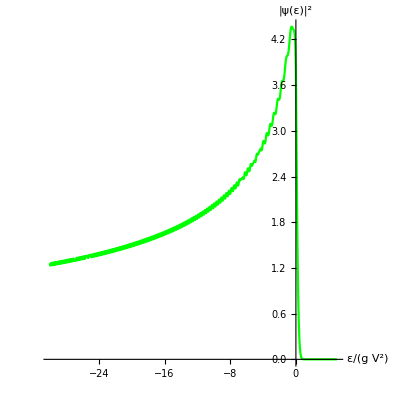

```mathematica
start =25;finish=-30;α=0.1;E2=-5;s122=ψ0[x]/.NDSolve[{0== E2 ψ0[x]-α ψ0''[x]+ψ0[x](Log[-x-I*10^(-5)]-9/(x-2+I*10^(-5)))+x ψ0[x],ψ0[start]==0,ψ0'[start]==0.001},ψ0,{x,start,finish}];nr2=(NIntegrate[Abs[s122^2],{x,finish,finish+0.5}]/0.5);
Plot[Abs[s122^2]/(8α nr2),{x,-30,5},PlotRange->All,AspectRatio->1,AxesLabel->{ε/(g V^2),"|ψ(ε)|^2"},PlotStyle->RGBColor[0,1,0]]
```

```mathematica
start =25;
finish=-30;
α=1;
E2=-5;
listoflists={};
For[j=0.1,j<0.21,j+=0.01,list={};For[i=1,i<10,i++,spick1=ψ0[x]/.NDSolve[{0== E2 ψ0[x]-j ψ0''[x]+ψ0[x](Log[-x-I*10^(-5)]-i/(x-2+I*10^(-5)))+x ψ0[x],ψ0[start]==0,ψ0'[start]==0.001},ψ0,{x,start,finish}];AppendTo[list,spick1]];AppendTo[listoflists,list]]
```

```mathematica
Table[NIntegrate[Abs[listoflists[[i]][[j]]]^2 ,{x,2,5}]/NIntegrate[Abs[listoflists[[i]][[j]]]^2,{x,0,2}],{i,10},{j,9}]
```

```mathematica
matrix10={{{0.003258728368043674},{0.39727252262808155},{31.0593237728409},{8.76836475042316},{0.25026575971567483},{0.007554682397197476},{0.0002584606129664839},{0.000013449488756703222},{5.549111081739026*^-7}},{{0.0042779088545012054},{0.41723034202266396},{35.39681129315836},{32.27183691920446},{0.8691359887836486},{0.03423847632012311},{0.00162695570568852},{0.00007806743551093733},{5.032485573601123*^-6}},{{0.005424164021623383},{0.43507677788350363},{32.8553515949974},{51.0857422116104},{3.265208972723448},{0.15168791356687422},{0.00872988539976335},{0.0005151584359774447},{0.000017313096110310017}},{{0.006688139888471084},{0.45083121128142306},{32.3499045136328},{116.91595679280596},{6.739525927845365},{0.4078050331688922},{0.026047691172987813},{0.001770045716163312},{0.00013392538995758116}},{{0.00806039622762991},{0.4656842474099263},{29.277362632944115},{162.07062536968292},{18.225217279225074},{0.9212309539582216},{0.08086214797986985},{0.0064850562536579335},{0.0005188264145605507}},{{0.009531380903314752},{0.4795473672142503},{27.344660337579743},{186.26272195840062},{60.38205924047428},{3.590632109682504},{0.2660175301761818},{0.021006879542019224},{0.002014353438102889}},{{0.01109218880948389},{0.49209842044955043},{25.107080433488566},{196.82256500147545},{110.40429282566407},{6.720254683389675},{0.742547129254841},{0.04207059638679661},{0.006303448873328801}},{{0.01273425340682082},{0.5037598576007283},{23.090312687890208},{196.6744767697832},{134.4272911514595},{17.059668428697353},{1.6106484542683295},{0.11146570829840384},{0.01500988887871642}},{{0.014449576041020106},{0.514645307243686},{21.358008540899064},{191.23189006363577},{203.56955835722937},{34.81030022342398},{3.0075475389731268},{0.38154187883522395},{0.040860944296010976}},{{0.01623071853927303},{0.5248874034643326},{19.78008032510749},{177.35832602293553},{235.5995304503825},{55.84509203463868},{8.920094311824512},{0.4670083217801124},{0.1164239239995173}}}
```

{{{0.00325873},{0.397273},{31.0593},{8.76836},{0.250266},{0.00755468},{0.000258461},{0.0000134495},{5.54911×10^-7}},{{0.00427791},{0.41723},{35.3968},{32.2718},{0.869136},{0.0342385},{0.00162696},{0.0000780674},{5.03249×10^-6}},{{0.00542416},{0.435077},{32.8554},{51.0857},{3.26521},{0.151688},{0.00872989},{0.000515158},{0.0000173131}},{{0.00668814},{0.450831},{32.3499},{116.916},{6.73953},{0.407805},{0.0260477},{0.00177005},{0.000133925}},{{0.0080604},{0.465684},{29.2774},{162.071},{18.2252},{0.921231},{0.0808621},{0.00648506},{0.000518826}},{{0.00953138},{0.479547},{27.3447},{186.263},{60.3821},{3.59063},{0.266018},{0.0210069},{0.00201435}},{{0.0110922},{0.492098},{25.1071},{196.823},{110.404},{6.72025},{0.742547},{0.0420706},{0.00630345}},{{0.0127343},{0.50376},{23.0903},{196.674},{134.427},{17.0597},{1.61065},{0.111466},{0.0150099}},{{0.0144496},{0.514645},{21.358},{191.232},{203.57},{34.8103},{3.00755},{0.381542},{0.0408609}},{{0.0162307},{0.524887},{19.7801},{177.358},{235.6},{55.8451},{8.92009},{0.467008},{0.116424}}}

```mathematica
matrix11=ArrayReshape[matrix10,{10,9}]
```

{{0.00325873,0.397273,31.0593,8.76836,0.250266,0.00755468,0.000258461,0.0000134495,5.54911×10^-7},{0.00427791,0.41723,35.3968,32.2718,0.869136,0.0342385,0.00162696,0.0000780674,5.03249×10^-6},{0.00542416,0.435077,32.8554,51.0857,3.26521,0.151688,0.00872989,0.000515158,0.0000173131},{0.00668814,0.450831,32.3499,116.916,6.73953,0.407805,0.0260477,0.00177005,0.000133925},{0.0080604,0.465684,29.2774,162.071,18.2252,0.921231,0.0808621,0.00648506,0.000518826},{0.00953138,0.479547,27.3447,186.263,60.3821,3.59063,0.266018,0.0210069,0.00201435},{0.0110922,0.492098,25.1071,196.823,110.404,6.72025,0.742547,0.0420706,0.00630345},{0.0127343,0.50376,23.0903,196.674,134.427,17.0597,1.61065,0.111466,0.0150099},{0.0144496,0.514645,21.358,191.232,203.57,34.8103,3.00755,0.381542,0.0408609},{0.0162307,0.524887,19.7801,177.358,235.6,55.8451,8.92009,0.467008,0.116424}}

```mathematica
list15={}
For[j=0.1,j<0.19,j+=0.01,For[i=0,i<9,i++;AppendTo[list15,{i+1,Log[Sqrt[j]],Log[matrix11[[Ceiling[1+(j-0.1)*100]]][[i]]]}]]]
```

{}

```mathematica
list15
```

{{2,-1.15129,-5.72642},{3,-1.15129,-0.923133},{4,-1.15129,3.4359},{5,-1.15129,2.17115},{6,-1.15129,-1.38523},{7,-1.15129,-4.88559},{8,-1.15129,-8.26077},{9,-1.15129,-11.2166},{10,-1.15129,-14.4045},{2,-1.10364,-5.45429},{3,-1.10364,-0.874117},{4,-1.10364,3.56662},{5,-1.10364,3.47419},{6,-1.10364,-0.140256},{7,-1.10364,-3.37441},{8,-1.10364,-6.42104},{9,-1.10364,-9.45794},{10,-1.10364,-12.1996},{2,-1.06013,-5.21689},{3,-1.06013,-0.832233},{4,-1.06013,3.49211},{5,-1.06013,3.93351},{6,-1.06013,1.18332},{7,-1.06013,-1.88593},{8,-1.06013,-4.741},{9,-1.06013,-7.57104},{10,-1.06013,-10.964},{2,-1.02011,-5.00742},{3,-1.02011,-0.796662},{4,-1.02011,3.47661},{5,-1.02011,4.76146},{6,-1.02011,1.90799},{7,-1.02011,-0.896966},{8,-1.02011,-3.64783},{9,-1.02011,-6.33675},{10,-1.02011,-8.91823},{2,-0.983056,-4.65317},{3,-0.983056,-0.734913},{4,-0.983056,3.30852},{5,-0.983056,5.22716},{6,-0.983056,4.10069},{7,-0.983056,1.27833},{8,-0.983056,-1.32419},{9,-0.983056,-3.86291},{10,-0.983056,-6.20746},{2,-0.94856,-4.50151},{3,-0.94856,-0.709077},{4,-0.94856,3.22315},{5,-0.94856,5.2823},{6,-0.94856,4.70415},{7,-0.94856,1.90513},{8,-0.94856,-0.297669},{9,-0.94856,-3.16841},{10,-0.94856,-5.06666},{2,-0.916291,-4.36346},{3,-0.916291,-0.685656},{4,-0.916291,3.13941},{5,-0.916291,5.28155},{6,-0.916291,4.90102},{7,-0.916291,2.83672},{8,-0.916291,0.476637},{9,-0.916291,-2.19404},{10,-0.916291,-4.19905},{2,-0.885978,-4.23709},{3,-0.885978,-0.664277},{4,-0.885978,3.06143},{5,-0.885978,5.25349},{6,-0.885978,5.31601},{7,-0.885978,3.54991},{8,-0.885978,1.10112},{9,-0.885978,-0.963535},{10,-0.885978,-3.19758},{2,-0.857399,-4.12085},{3,-0.857399,-0.644572},{4,-0.857399,2.98468},{5,-0.857399,5.17817},{6,-0.857399,5.46213},{7,-0.857399,4.02258},{8,-0.857399,2.18831},{9,-0.857399,-0.761408},{10,-0.857399,-2.15052}}

```mathematica
plt=ListPlot3D[list15,AxesLabel->{ "(|SubscriptBox[v, s]|)^2/(g SuperscriptBox[V, 2])^2","Log((√α)/(g SuperscriptBox[V, 2]))","Log((∫_E_0^∞)/(∫_0^E_0))"},AxesStyle->Italic,InterpolationOrder->10,Boxed->False,PlotLabel->"E_0/(g SuperscriptBox[V, 2])=5, E_s/(g SuperscriptBox[V, 2])=2"]
```

-Graphics3D-

```mathematica
Export["figure15.eps",-Graphics3D-]
```

figure15.eps

```mathematica
Table[NIntegrate[x Abs[listoflists[[i]][[j]]]^2 ,{x,0,2}]/NIntegrate[Abs[listoflists[[i]][[j]]]^2,{x,0,2}],{i,10},{j,9}]
```

```mathematica
matrix10={{{0.24763180310647673},{0.24230155027507255},{0.43173292088774745},{0.24581136412830354},{0.20153398416271234},{0.18851103116776524},{0.17543597109129896},{0.16190259708636603},{0.14852765413975105}},{{0.25847784549525404},{0.2533176746380054},{0.4925133188877273},{0.3539274575267768},{0.21112679636614065},{0.1956979152998425},{0.18172350383173796},{0.1673846472368637},{0.15336427840239103}},{{0.26878494820013554},{0.2638328010540143},{0.5036036834662184},{0.45730499824335963},{0.22560696916760453},{0.2025990299493588},{0.1875615113919292},{0.17245391489886883},{0.15784382183201617}},{{0.27862160308612866},{0.27390719516365},{0.5283884494165043},{0.7995132337965134},{0.24408206601952565},{0.20941577315980248},{0.19301583100017125},{0.17716696977152002},{0.1620170876554444}},{{0.2880424296219864},{0.28361259248559323},{0.5284801602834768},{1.0807934167736626},{0.2902993997794015},{0.21653317306549652},{0.19818352695133468},{0.18157301442249463},{0.16592494245654987}},{{0.29709161877198553},{0.29298753238204084},{0.5355169011696217},{1.2776202704120645},{0.4498805077366587},{0.2288077178935247},{0.2032870645996688},{0.1857195062928742},{0.16960151468723011}},{{0.30580547797063146},{0.302055643911777},{0.5366159575266614},{1.410863982868967},{0.6576016768769},{0.24282520862512283},{0.2087194824368193},{0.18963551561084466},{0.17307638498914862}},{{0.3142141403440589},{0.3108517857598466},{0.5370716260122269},{1.4844547565564312},{0.7836569378175876},{0.27764653821144336},{0.21481847619703495},{0.19341596731825877},{0.1763750267527264}},{{0.32234297027431597},{0.3193995830117457},{0.5380843336718271},{1.5227557784194603},{1.1098834458439153},{0.33727084912615296},{0.22204479833846388},{0.19735371379492056},{0.17953474457011098}},{{0.33021349606465245},{0.32771980474416285},{0.5386120520516617},{1.4987434894090312},{1.302024413453832},{0.4123733730846997},{0.23977516665969817},{0.20083701622664643},{0.18262180750358803}}}
```

{{{0.247632},{0.242302},{0.431733},{0.245811},{0.201534},{0.188511},{0.175436},{0.161903},{0.148528}},{{0.258478},{0.253318},{0.492513},{0.353927},{0.211127},{0.195698},{0.181724},{0.167385},{0.153364}},{{0.268785},{0.263833},{0.503604},{0.457305},{0.225607},{0.202599},{0.187562},{0.172454},{0.157844}},{{0.278622},{0.273907},{0.528388},{0.799513},{0.244082},{0.209416},{0.193016},{0.177167},{0.162017}},{{0.288042},{0.283613},{0.52848},{1.08079},{0.290299},{0.216533},{0.198184},{0.181573},{0.165925}},{{0.297092},{0.292988},{0.535517},{1.27762},{0.449881},{0.228808},{0.203287},{0.18572},{0.169602}},{{0.305805},{0.302056},{0.536616},{1.41086},{0.657602},{0.242825},{0.208719},{0.189636},{0.173076}},{{0.314214},{0.310852},{0.537072},{1.48445},{0.783657},{0.277647},{0.214818},{0.193416},{0.176375}},{{0.322343},{0.3194},{0.538084},{1.52276},{1.10988},{0.337271},{0.222045},{0.197354},{0.179535}},{{0.330213},{0.32772},{0.538612},{1.49874},{1.30202},{0.412373},{0.239775},{0.200837},{0.182622}}}

```mathematica
matrix11=ArrayReshape[matrix10,{10,9}]
```

{{0.247632,0.242302,0.431733,0.245811,0.201534,0.188511,0.175436,0.161903,0.148528},{0.258478,0.253318,0.492513,0.353927,0.211127,0.195698,0.181724,0.167385,0.153364},{0.268785,0.263833,0.503604,0.457305,0.225607,0.202599,0.187562,0.172454,0.157844},{0.278622,0.273907,0.528388,0.799513,0.244082,0.209416,0.193016,0.177167,0.162017},{0.288042,0.283613,0.52848,1.08079,0.290299,0.216533,0.198184,0.181573,0.165925},{0.297092,0.292988,0.535517,1.27762,0.449881,0.228808,0.203287,0.18572,0.169602},{0.305805,0.302056,0.536616,1.41086,0.657602,0.242825,0.208719,0.189636,0.173076},{0.314214,0.310852,0.537072,1.48445,0.783657,0.277647,0.214818,0.193416,0.176375},{0.322343,0.3194,0.538084,1.52276,1.10988,0.337271,0.222045,0.197354,0.179535},{0.330213,0.32772,0.538612,1.49874,1.30202,0.412373,0.239775,0.200837,0.182622}}

```mathematica
list15={}
For[j=0.1,j<0.19,j+=0.01,For[i=0,i<9,i++;AppendTo[list15,{Log[Sqrt[j]],i+1,1/matrix11[[Ceiling[1+(j-0.1)*100]]][[i]]}]]]
```

{}

```mathematica
list15
```

{{-1.15129,2,4.03825},{-1.15129,3,4.12709},{-1.15129,4,2.31625},{-1.15129,5,4.06816},{-1.15129,6,4.96194},{-1.15129,7,5.30473},{-1.15129,8,5.70009},{-1.15129,9,6.17655},{-1.15129,10,6.73275},{-1.10364,2,3.8688},{-1.10364,3,3.94761},{-1.10364,4,2.0304},{-1.10364,5,2.82544},{-1.10364,6,4.73649},{-1.10364,7,5.10992},{-1.10364,8,5.50287},{-1.10364,9,5.97426},{-1.10364,10,6.52042},{-1.06013,2,3.72045},{-1.06013,3,3.79028},{-1.06013,4,1.98569},{-1.06013,5,2.18672},{-1.06013,6,4.43249},{-1.06013,7,4.93586},{-1.06013,8,5.33158},{-1.06013,9,5.79865},{-1.06013,10,6.33538},{-1.02011,2,3.5891},{-1.02011,3,3.65087},{-1.02011,4,1.89255},{-1.02011,5,1.25076},{-1.02011,6,4.09698},{-1.02011,7,4.77519},{-1.02011,8,5.18092},{-1.02011,9,5.64439},{-1.02011,10,6.17219},{-0.983056,2,3.36597},{-0.983056,3,3.41311},{-0.983056,4,1.86735},{-0.983056,5,0.782705},{-0.983056,6,2.22281},{-0.983056,7,4.37048},{-0.983056,8,4.91915},{-0.983056,9,5.38446},{-0.983056,10,5.89617},{-0.94856,2,3.27005},{-0.94856,3,3.31065},{-0.94856,4,1.86353},{-0.94856,5,0.708786},{-0.94856,6,1.52068},{-0.94856,7,4.11819},{-0.94856,8,4.79112},{-0.94856,9,5.27327},{-0.94856,10,5.7778},{-0.916291,2,3.18254},{-0.916291,3,3.21697},{-0.916291,4,1.86195},{-0.916291,5,0.673648},{-0.916291,6,1.27607},{-0.916291,7,3.6017},{-0.916291,8,4.65509},{-0.916291,9,5.1702},{-0.916291,10,5.66974},{-0.885978,2,3.10229},{-0.885978,3,3.13087},{-0.885978,4,1.85844},{-0.885978,5,0.656704},{-0.885978,6,0.900996},{-0.885978,7,2.96498},{-0.885978,8,4.5036},{-0.885978,9,5.06704},{-0.885978,10,5.56995},{-0.857399,2,3.02834},{-0.857399,3,3.05139},{-0.857399,4,1.85662},{-0.857399,5,0.667226},{-0.857399,6,0.768035},{-0.857399,7,2.42499},{-0.857399,8,4.17057},{-0.857399,9,4.97916},{-0.857399,10,5.4758}}

```mathematica
plt=ListPlot3D[list15,AxesLabel->{ "Log((√α)/(g SuperscriptBox[V, 2]))","(|SubscriptBox[v, s]|)^2/(g SuperscriptBox[V, 2])^2","g V^2/((SubsuperscriptBox[∫, 0, SubscriptBox[E, 0]/2]ε SuperscriptBox[|ψ[ε]|, 2] ⅆε)/(∫_0^E_0))"},AxesStyle->Italic,InterpolationOrder->10,Boxed->False,PlotLabel->"E_0/(g SuperscriptBox[V, 2])=5, E_s/(g SuperscriptBox[V, 2])=2"]
```

-Graphics3D-

```mathematica
Export["figure14.eps",-Graphics3D-]
```

figure14.eps